```mathematica
gg = {1};
For[i =0, i<10000, i++, AppendTo[gg,(Last[gg])/(1+0.01 Last[gg])]];
```

```mathematica
gg[[2500]]
```

0.0285796

```mathematica
Last[gg]
```

0.00990099

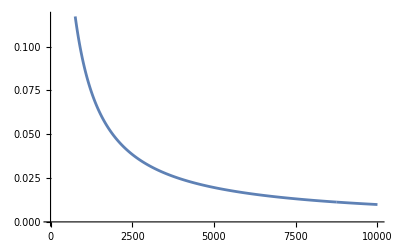

```mathematica
ListLinePlot[gg]
```

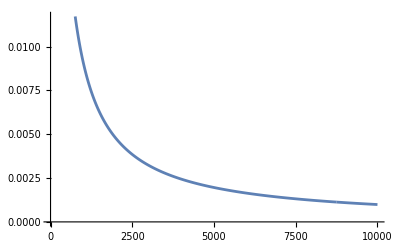

```mathematica
ListLinePlot[gg]
```